# Plotting the Characteristics of First Order PDE

## Question1: Ut + x Ux = 0

```mathematica
sol1=DSolve[{t'[s]==1,x'[s]==x[s],u'[s]==0},{t[s],x[s],u[s]},s]
```

{{t[s]→s+C[1],x[s]→ⅇ^s C[2],u[s]→C[3]}}

```mathematica
table1=Table[{t[s],x[s],u[s]}/.sol1/.{C[1]->1,C[2]->2,C[3]->3}]
```

{{1+s,2 ⅇ^s,3}}

```mathematica
Plot[table1,{s,-5,5},PlotLegends->"Expressions",PlotTheme->"Marketing"]
```

-Graphics-

## Question2: x Ux + yUy = 0

```mathematica
c1=D[x[t],t]==x[t]
c2=D[y[t],t] == y[t]
c3=D[u[t],t]==0
```

x'[t]==x[t]

y'[t]==y[t]

u'[t]==0

```mathematica
sol2=DSolve[{c1,c2,c3},{x[t],y[t],u[t]},t]
```

{{x[t]→ⅇ^t C[1],y[t]→ⅇ^t C[2],u[t]→C[3]}}

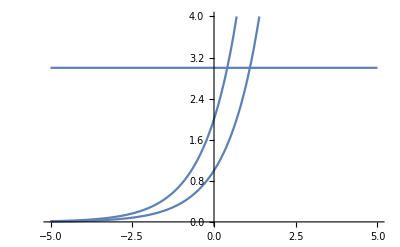

```mathematica
Plot[{x[t],y[t],u[t]}/.sol2/.{C[1]->1,C[2]->2,C[3]->3},{t,-5,5},PlotRange->{0,4}]
```

## Question3: Ux+Uy==1; {s:[-10,10]; C=[1,2,3]}

```mathematica
sol3=DSolve[{x'[s]==1,y'[s]==1,u'[s]==1},{x[s],y[s],u[s]},s]
```

{{x[s]→s+C[1],y[s]→s+C[2],u[s]→s+C[3]}}

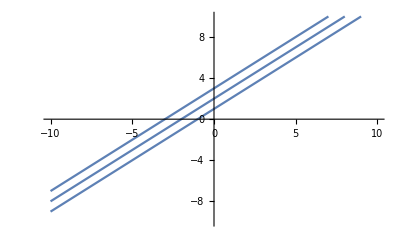

```mathematica
Plot[{x[s],y[s],u[s]}/.sol3/.{C[1]->1,C[2]->2,C[3]->3},{s,-10,10},PlotRange->{-10,10}]
```

## Question4: Ux+Uy=Sin[x]; s[-10,10]

```mathematica
sol4=DSolve[{x'[s]==1,y'[s]==1,u'[s]==Sin[x[s]]},{x[s],y[s],u[s]},s]
```

{{x[s]→s+C[1],u[s]→C[2]-Cos[s] Cos[C[1]]+Sin[s] Sin[C[1]],y[s]→s+C[3]}}

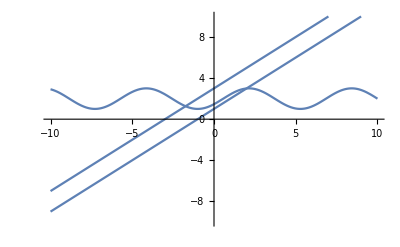

```mathematica
Plot[{x[s],y[s],u[s]}/.sol4/.{C[1]->1,C[2]->2,C[3]->3},{s,-10,10},PlotRange->{-10,10}]
```